# Study of the dependance of the Regge trajectory slope with respect to the model’s parameter.

Now let’s study how the slope of the Regge trajectory changes with a or with b. To achieve so let’s compute the slope for several values of a and b.

```mathematica
F[V_Symbol]:=-S''[z]+V[z]*S[z];
V[A_Symbol,ϕ_Symbol]:=(3*D[D[A[z],z],z]+3/z^2-D[D[ϕ[z],z],z])/2+(3*D[A[z],z]-3/z-D[ϕ[z],z])^2/4;
```

We define the face space of  and the values of the parameters.

```mathematica
z0values=Table[z0,{z0,0.5,10,0.1}];
paramvalues=Table[a,{a,0.1,1.5,0.1}];
```

## Model A

Build the differential operator for model A

```mathematica
Ae1[z_]:=-a*z^2;
ϕe1[z_]:=z*Sqrt[3*a*(3+2*a*z^2)]+3/2*Sqrt[6]ArcSinh[Sqrt[2*a/3]*z];
S11=Ae1[z]-Sqrt[1/6]*ϕe1[z];
S12=Sqrt[8/3]*ϕe1[z];
As1[z_]:=S11;
ϕs1[z_]:=S12;
v1=V[As1,ϕs1];
Z1[z_]:=v1;
```

Get the first 4 eigenvalues for every value of  and the parameter.

```mathematica
eigenA=Table[Table[NDEigenvalues[F[Z1],S[z],{z,0,z0},4],{z0,0.5,10,0.1}],{a,0.1,1.5,0.1}];
```

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix … in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

General::stop: Further output of Eigensystem::chnpdef will be suppressed during this calculation.

Get  for each value of the parameter.

```mathematica
trajectoriesA=Table[Table[Table[{n,Extract[Extract[Extract[eigenA,a],z0],n]},{n,1,4}],{z0,1,Length[z0values]}],{a,1,Length[paramvalues]}];
R2A=Table[Table[LinearModelFit[Extract[Extract[trajectoriesA,a],z0],x,x]["RSquared"],{z0,1,Length[z0values]}],{a,1,Length[paramvalues]}];
z0maxA=Table[Extract[Extract[Extract[Table[MaximalBy[Table[{Extract[z0values,i],Extract[Extract[R2A,a],i]},{i,1,Length[z0values]}],Last],{a,1,Length[paramvalues]}],j],1],1],{j,1,Length[paramvalues]}];
```

{5.2,3.7,3.,2.6,2.3,2.1,2.,1.9,1.8,1.7,1.6,1.5,4.3,1.4,4.}

Get the slope for every value of the parameter.

```mathematica
eigenAopt=Diagonal[Table[NDEigenvalues[F[Z1],S[z],{z,0,z0},4],{z0,z0maxA},{a,0.1,1.5,0.1}]];
```

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix … in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

General::stop: Further output of Eigensystem::chnpdef will be suppressed during this calculation.

Let’s see which is the behavior.

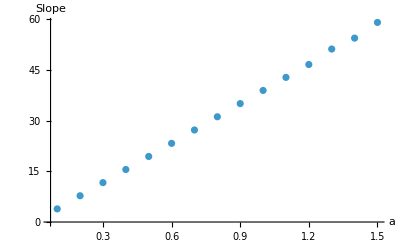

```mathematica
slopesA=Table[{Extract[paramvalues,i],LinearModelFit[Extract[eigenAopt,i],x,x]["ParameterEstimates"][2,"BestFitParameter"]},{i,1,Length[paramvalues]}];
ListPlot[slopesA,PlotRange->All,AxesLabel->{"a","Slope"}]
```

We see that the behavior is linear as we expected dimensionally, as the parameters have the same dimension as the masses squared. Let’s see now what is the relation:

```mathematica
lmsA=LinearModelFit[slopesA,x,x];
lmsA["ParameterEstimates"]
lmsA["RSquared"]
```

0.999867

Now let’s do the same also for the initial mass:

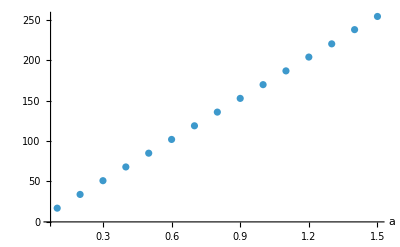

0.999994

```mathematica
m0A=Table[{Extract[paramvalues,i],LinearModelFit[Extract[eigenAopt,i],x,x]["ParameterEstimates"][1,"BestFitParameter"]},{i,1,Length[paramvalues]}];
ListPlot[m0A,PlotRange->All,AxesLabel->{"a",""}]
lmmA=LinearModelFit[m0A,x,x];
lmmA["ParameterEstimates"]
lmmA["RSquared"]
```

## Model B

Build the differential operator for model B.

```mathematica
Ae2[z_]:=-Log[(2^(3/8)*3^(1/8)*Gamma[5/4]*BesselI[1/4,(b*z^2)/(Sqrt[6])])/(b^(1/4)*Sqrt[z])];
ϕe2[z_]:=b*z^2;
S21=Ae2[z]-Sqrt[1/6]*ϕe2[z];
S22=Sqrt[8/3]*ϕe2[z];
As2[z_]:=S21;
ϕs2[z_]:=S22;
v2=V[As2,ϕs2];
Z2[z_]:=v2;
```

Get the first 4 eigenvalues for every value of  and the parameter.

```mathematica
eigenB=Table[Table[NDEigenvalues[F[Z2],S[z],{z,0,z0},4],{z0,0.5,10,0.1}],{b,0.1,1.5,0.1}];
```

Get  for each value of the parameter.

```mathematica
trajectoriesB=Table[Table[Table[{n,Extract[Extract[Extract[eigenB,b],z0],n]},{n,1,4}],{z0,1,Length[z0values]}],{b,1,Length[paramvalues]}];
R2B=Table[Table[LinearModelFit[Extract[Extract[trajectoriesB,b],z0],x,x]["RSquared"],{z0,1,Length[z0values]}],{b,1,Length[paramvalues]}];
z0maxB=Table[Extract[Extract[Extract[Table[MaximalBy[Table[{Extract[z0values,i],Extract[Extract[R2B,b],i]},{i,1,Length[z0values]}],Last],{b,1,Length[paramvalues]}],j],1],1],{j,1,Length[paramvalues]}];
```

Get the slope for every value of the parameter.

```mathematica
eigenBopt=Diagonal[Table[NDEigenvalues[F[Z2],S[z],{z,0,z0},4],{z0,z0maxB},{b,0.1,1.5,0.1}]];
```

Let’s see which is the behavior.

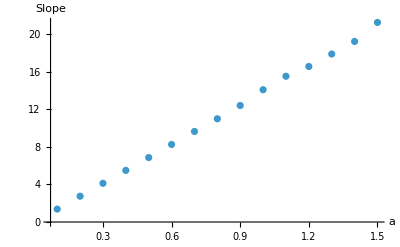

0.999305

```mathematica
slopesB=Table[{Extract[paramvalues,i],LinearModelFit[Extract[eigenBopt,i],x,x]["ParameterEstimates"][2,"BestFitParameter"]},{i,1,Length[paramvalues]}];
ListPlot[slopesB,PlotRange->All,AxesLabel->{"a","Slope"}]
lmsB=LinearModelFit[slopesB,x,x];
lmsB["ParameterEstimates"]
lmsB["RSquared"]
```

Now let’s do the same also for the initial mass:

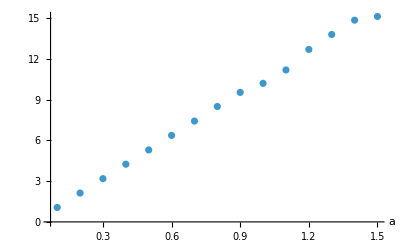

0.997981

```mathematica
m0B=Table[{Extract[paramvalues,i],LinearModelFit[Extract[eigenBopt,i],x,x]["ParameterEstimates"][1,"BestFitParameter"]},{i,1,Length[paramvalues]}];
ListPlot[m0B,PlotRange->All,AxesLabel->{"a",""}]
lmmB=LinearModelFit[m0B,x,x];
lmmB["ParameterEstimates"]
lmmB["RSquared"]
```